## Figure 3C, 3D (p=3 nutrients)

Evaluate notebook to generate plots for Fig. 3C, D (the oligotroph condition for p=3 nutrients)

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
s1List={0.1,0.15,0.2,0.25,0.3,0.4,0.5,0.6,0.7};
nameStringList=Table["="<>ToString[s1List[[i]]],{i,Length[s1List]}];
nameStringList=Join[nameStringList,{"symm"}];
numTests=Length[nameStringList];
```

```mathematica
namePt1="data//3nutrients//statisticalCoexistence_pbc_m20__d=1_l=Sqrt[10]_s1";
namePt2="_p3_fixedPoints_s_alphas.mx";
```

### get colorscheme data

```mathematica
(*Read in the numerical data*)Get["https://pastebin.com/raw/gN4wGqxe"]
ParulaCM=With[{colorlist=RGBColor@@@parulaColors},Blend[colorlist,#]&];
Cube1CM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
CubeYFCM=With[{colorlist=RGBColor@@@cubeYFColors},Blend[colorlist,#]&];
LinearLCM=With[{colorlist=RGBColor@@@cube1Colors},Blend[colorlist,#]&];
JetCM=With[{colorlist=RGBColor@@@jetColors},Blend[colorlist,#]&];
```

### Iteratively import data

```mathematica
fixedPoints={};
s={};
alphas={};
```

```mathematica
For[i=1,i≤numTests,i++,
name=namePt1<>nameStringList[[i]]<>namePt2;
thisData=Import[name];
fixedPoints=Join[fixedPoints,{thisData[[1]]}];
s=Join[s,{thisData[[2]]}];
alphas=Join[alphas,{thisData[[3]]}];

];
m=Length[alphas[[1,1]]];
numTrials=Length[alphas[[1]]];
```

```mathematica
e=1;
supply=1;
```

### calculate M=effective number of species, and plot distributions

```mathematica
shannonEntropy[n_]:=
Module[{modN,entropyTable,entropyTable2,entropy},
modN=n/.{x_/;x<0->0};
entropyTable=Table[-modN[[i]]*Log[modN[[i]]],{i,Length[modN]}]//Quiet;
entropyTable2=entropyTable/.{Indeterminate->0};
entropy=entropyTable2//Total
]
```

Shannon entropy is insensitive to cutoffs, super rare species

```mathematica
total=Sqrt[10];
```

```mathematica
entropy=ConstantArray[0,numTests];
entropyHist=ConstantArray[0,numTests];
effectiveSpecies=ConstantArray[0,numTests];
```

```mathematica
For[i=1,i<=numTests,i++,
proportionalFP=Table[fixedPoints[[i,j]]/total,{j,numTrials}];
entropy[[i]]=Table[shannonEntropy[proportionalFP[[k]]],{k,numTrials}];
effectiveSpecies[[i]]=Table[E^entropy[[i,k]],{k,numTrials}];

]
```

```mathematica
includedHist={1,2,3,4,5};
plottingSpecies=effectiveSpecies[[includedHist]];
includedS=s[[includedHist,1]];
colors=ParulaCM/@((includedS-includedS[[1]])/(includedS[[-1]]-includedS[[1]]));
```

```mathematica
threeDCoords=Table[Table[{includedS[[i]],plottingSpecies[[i,j]]},{j,Length[plottingSpecies[[i]]]}],{i,Length[includedHist],1,-1}];
```

```mathematica
plotColors=colors//Reverse;
```

```mathematica
Histogram3D[threeDCoords,{{.007},{1}},"Probability",Boxed->False,ScalingFunctions->{"Reverse",Identity,Identity},TicksStyle->Black,ViewPoint->{2.8770859632354266,1.3997211835038195,1.1014340509555465},AxesEdge->{{0,1},Automatic,Automatic},ChartStyle->plotColors,LabelStyle->Directive[Black,14]]
```

-Graphics3D-

```mathematica
Export["fig3C_3nutrients_diversityDistribution.png",%,ImageResolution->600];
```

### diverse strategies

```mathematica
mapToSimplex[point_]:=
Module[{},
newX=point[[2]]-point[[1]];
newY=Sqrt[3]*point[[3]];
{newX,newY}
];
```

```mathematica
trial=3;
diverseS=s[[trial]];

cutoff=Quantile[effectiveSpecies[[trial]],.9];
diversePositions=Position[effectiveSpecies[[trial]],x_/;x≥cutoff];
diverseAlphas=Flatten[Table[alphas[[trial,diversePositions[[i]]]],{i,Length[diversePositions]}],2];
```

```mathematica
remappedStrats=Table[mapToSimplex[diverseAlphas[[i]]],{i,Length[diverseAlphas]}];
```

```mathematica
pointPlot=ListPlot[remappedStrats,PlotRange->{{-1,1},{0,Sqrt[3]}},Axes->False,PlotStyle->Darker[ColorData[97,2]],AspectRatio->Sqrt[3]/2];
```

```mathematica
regionSol=Solve[diverseS[[1]]/x+diverseS[[2]]/y+diverseS[[3]]/z==3&&x+y+z==1,{x,y,z}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
regionParametricFunction1[x_]={x,y,z}/.regionSol[[1]];
regionParametricFunction2[x_]={x,y,z}/.regionSol[[2]];
```

```mathematica
regionPlot=ParametricPlot[{mapToSimplex[regionParametricFunction1[x]],mapToSimplex[regionParametricFunction2[x]]},{x,.01,1},PlotStyle->{Directive[ColorData[97,1]//Darker,Thick,Dashed],Directive[ColorData[97,1]//Darker,Thick,Dashed]}];
```

```mathematica
supplyPoint=mapToSimplex[diverseS];
```

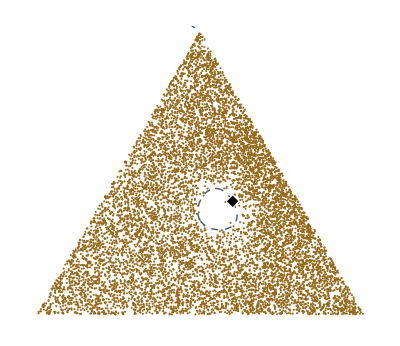

```mathematica
Show[pointPlot,regionPlot,Graphics[{EdgeForm[{White}],Polygon[{supplyPoint+{-.04,0},supplyPoint+{0,.04},supplyPoint+{.04,0},supplyPoint+{0,-.04}}]}]]
```

```mathematica
Export["fig3D_3nutrients_diverseStrategies.svg",%];
```